# Steiner's tree problem

## In large graphs

## Description

Steiner's tree problem
Input data:
G – undirected graph,
c : E(G) → R^+ – edge weight function,
T ⊆ V(G) – set of terminals
Output data:
steiner's tree for T in G.
i.e. output is G' – tree-subgraph of G : T ⊆ V(G') ∧ c(E(G')) → min.

## Utility Functions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll[clearAndProtect]

SetAttributes[clearAndProtect, {HoldAll, Listable}]

clearAndProtect[what_Symbol]:=
(Unprotect[what];
ClearAll[what];
Protect[what];)
```

## Graph Utility Functions

```mathematica
ClearAll[vertexDegree]

vertexDegree[vert_, edges_] := Count[edges, x_/;MemberQ[x, vert]]
```

```mathematica
ClearAll[edgeWeight]

edgeWeight[graph_Graph, edge_]:=PropertyValue[{graph, edge}, EdgeWeight]
```

```mathematica
ClearAll[edgeWeightSum]

edgeWeightSum[edges_List, weights_Association]:=Total[Lookup[weights, #]&/@edges]
```

## Needs

```mathematica
Needs["Steiner`Generator`", "packages\\steiner_generator.wl"]
Needs["Steiner`SteinLib`", "packages\\steiner_steinlib.wl"]
```

graph::shdw: Symbol graph appears in multiple contexts {Steiner`Generator`,Global`}; definitions in context Steiner`Generator` may shadow or be shadowed by other definitions.

x::shdw: Symbol x appears in multiple contexts {Steiner`SteinLib`,Global`}; definitions in context Steiner`SteinLib` may shadow or be shadowed by other definitions.

x$::shdw: Symbol x$ appears in multiple contexts {Steiner`SteinLib`,Global`}; definitions in context Steiner`SteinLib` may shadow or be shadowed by other definitions.

## Input data

### Generator

#### 15

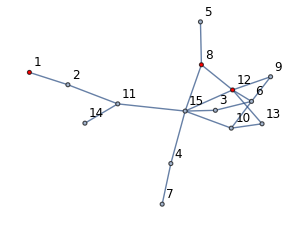

```mathematica
{graph15, weightAssociation15, terminals15} = generateSteinerProblemInstance[15, 3, BernoulliProbability->0.125];
drawGraph[graph15, terminals15, VertexLabelStyle->Directive[Black,12]]
```

#### 100

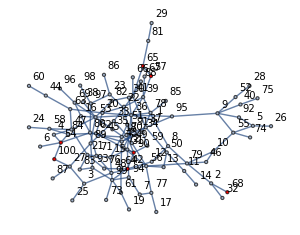

```mathematica
{graph100, weightAssociation100, terminals100} = generateSteinerProblemInstance[100, 7, BernoulliProbability->0.023];
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,10]]
```

### SteinLib

```mathematica
(*!*)
getInstancesList["\\steinlib\\D"]
```

{}

#### d10

```mathematica
{stlibTestGraph, stlibTestWeights, stlibTestTerminals} = importSteinLibInstance["\\steinlib\\D\\d10.stp"];
```

## Visualization

### Basic visualization

#### Functions

```mathematica
ClearAll[terminalVertexStyle]

terminalVertexStyle[terminals_]:=(#->{Red}&/@terminals)
```

```mathematica
ClearAll[voronoiVertexStyle]

voronoiVertexStyle[vertexList_, snm_List]:=
Composition[
Thread[vertexList->#]&,
snm/.#&,
Thread[#->ColorData["SunsetColors"]/@Range[0, 0.9, 0.9/(Length@# - 1)]]&,
DeleteDuplicates[snm]&
][]
```

```mathematica
ClearAll[drawGraph]
clearAndProtect@VertexStyleFunc

Options[drawGraph] = Join[Options[Graph], {VertexStyleFunc->terminalVertexStyle}];

"Draws graph and highlights terminalVertices.";
drawGraph[graph_Graph, vertexStyleInput__, opts:OptionsPattern[]]:= 
Graph[graph,
{FilterRules[{opts}, Options[Graph]],
VertexStyle->(Evaluate[OptionValue[VertexStyleFunc][vertexStyleInput]]),
VertexLabels->Automatic,
VertexLabelStyle->Directive[Black,10],
EdgeLabels->Placed["EdgeWeight", Tooltip],
ImageSize->300
}
]
```

```mathematica
ClearAll[drawGraphSubgraph]

"Highlights subgraphEdges in graph.";
Options[drawGraphSubgraph] = Options[Graph];

drawGraphSubgraph[graph_Graph, subgraphEdges_, terminalVertices_,  opts:OptionsPattern[]]:= 
drawGraph[graph,terminalVertices,
EdgeStyle->(#->{Orange, Thickness[0.015]}&/@subgraphEdges),
FilterRules[{opts}, Options[drawGraph]]]
```

```mathematica
ClearAll[gridResult]

gridResult[graph_Graph,  terminals_, tree_, treeWeight_]:=Grid[{{"Graph", "Tree" , "Tree weight"},
{drawGraphSubgraph[graph, tree, terminals],
drawGraph[Graph[tree], terminals, ImageSize->100],
treeWeight}}, Frame->All]
```

### Examples

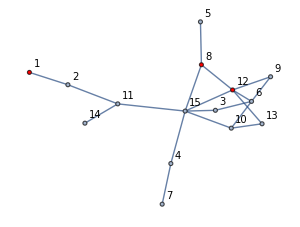

```mathematica
drawGraph[graph15, terminals15, VertexLabelStyle->Directive[Black,10]]
```

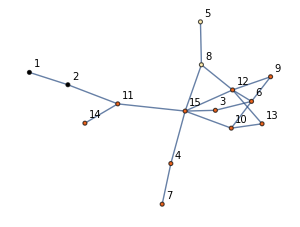

```mathematica
drawGraph[graph15, VertexList@graph15, Normal[dijkstraVoronoi[graph15, terminals15]["voronoi"]], VertexLabelStyle->Directive[Black,10], VertexStyleFunc->voronoiVertexStyle]
```

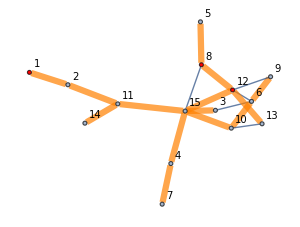

```mathematica
drawGraphSubgraph[graph15, FindSpanningTree[graph15]//EdgeList, terminals15, VertexLabelStyle->Directive[Black,10]]
```

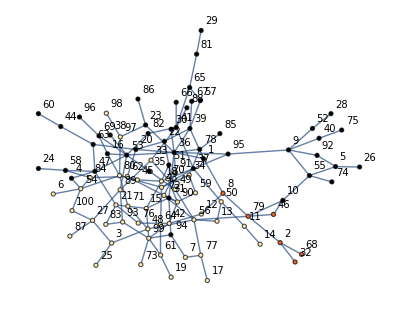

```mathematica
drawGraph[graph100, VertexList@graph100, Normal[dijkstraVoronoi[graph100, terminals15]["voronoi"]], VertexLabelStyle->Directive[Black,10], VertexStyleFunc->voronoiVertexStyle]
```

## Voronoi Diagram

```mathematica
ClearAll[dijkstraVoronoi]

dijkstraVoronoi[graph_Graph, terminals_]:=
Module[
{
spValue = CreateDataStructure["FixedArray", Infinity, VertexCount[graph]],
ancestors = CreateDataStructure["FixedArray", Infinity, VertexCount[graph]],
voronoiCenter = CreateDataStructure["FixedArray", Infinity, VertexCount[graph]],
used = CreateDataStructure["BitVector", VertexCount[graph] + 1],
heap = CreateDataStructure["PriorityQueue"],
curVert, curWeight
},

(spValue["SetPart", #, 0]; ancestors["SetPart", #, -1];
voronoiCenter["SetPart", #, #]; heap["Push", {0, #}];)&/@terminals;

While[True,
If[heap["EmptyQ"], Break[]];
{curWeight, curVert} = heap["Pop"];
curWeight *= -1;
If[used["BitTest", curVert], Continue[], used["BitSet", curVert]];
Scan[
If[!used["BitTest", #] ∧ spValue["Part", #] > curWeight + edgeWeight[graph, curVert<->#],
(heap["Push", {-edgeWeight[graph, curVert<->#], #}];
ancestors["SetPart", #, curVert];
voronoiCenter["SetPart", #, voronoiCenter["Part", curVert]];
spValue["SetPart", #, curWeight + edgeWeight[graph, curVert<->#]])]&,
AdjacencyList[graph, curVert]
]
];

<|"distance" -> spValue, "ancestors" -> ancestors, "used" -> used, "voronoi" -> voronoiCenter|>
]
```

```mathematica
ClearAll[repairVoronoi]

repairVoronoi[] := 1
```

## Exact algorithms

### Dynamic programming (Dreyfus – Wagner) [1][3][4][5]

#### Description

Asymptotic time is : O (3^t n+2^t n^2), where t = #Terminals. n = #Vertices.

#### Functions

```mathematica
ClearAll[DEFrunDreyfusWagnerQStep]

(* Internal cycle for q values *)
DEFrunDreyfusWagnerQStep[]:=
(runDreyfusWagnerQStep[size_]:=
Module[
{terminalSubsets = Sort/@Subsets[terminals, {size}]},

Scan[
Function[U,
Scan[
Function[x,
q[Union[U, {x}], x] = Infinity;

(* min cycle *)
(tmpMin = (p[Union[#, {x}]]+p[Union[Complement[U, #], {x}]]);
If[q[Union[U, {x}], x]>tmpMin,
q[Union[U, {x}], x] = tmpMin;
qAnc[Union[U, {x}], x] = {"q", {Union[#, {x}], Union[Complement[U, #], {x}]}}]
)&/@Subsets[U, {1, size-1}]

][#]&,
Complement[vertList, U]]
][#]&,
terminalSubsets];
];)
```

```mathematica
ClearAll[DEFrunDreyfusWagnerPStep]

(* Internal cycle for p values *)
DEFrunDreyfusWagnerPStep[]:=
(runDreyfusWagnerPStep[size_]:=
Module[
{terminalSubsets = Sort/@Subsets[terminals, {size}]},

Scan[
Function[U, Scan[
Function[x,
p[Union[U, {x}]] = Infinity;

(* first min cycle *)
(tmpMin = (p[U] + distMatrix⟦x, #⟧);
If[p[Union[U, {x}]]>tmpMin,
p[Union[U, {x}]] = tmpMin;
pAnc[Union[U, {x}]] = {"pp", {U,{x, #}}}]
)&/@U;

(* second min cycle *)
(tmpMin = (q[Union[U, {#}], #]+ distMatrix⟦x, #⟧);
If[p[Union[U, {x}]]>tmpMin,
p[Union[U, {x}]] = tmpMin;
pAnc[Union[U, {x}]] = {"pq",{{Union[U, {#}], #} , {x, #}}}]
)&/@Complement[vertList, U];

][#]&,
Complement[vertList, U]]
][#]&,
terminalSubsets];
];)
```

```mathematica
ClearAll[DEFrestoredTreeDreyfusWagner]

(* Tree resroration *)
DEFrestoredTreeDreyfusWagner[]:=
(restoredTreeDreyfusWagner[]:=
Composition[
DeleteDuplicates[#, Sort@#1==Sort@#2&]&,
Flatten@#&,
Map[UndirectedEdge@@@Partition[#, 2, 1]&, #,{-2}]&
][restoredTreeDreyfusWagner[pAnc[Sort@terminals]]];

restoredTreeDreyfusWagner[{mark_, ancestor_}]:=
Switch[mark,
"sp",ancestor,
"q",restoredTreeDreyfusWagner[pAnc[#]]&/@ancestor,
"pp",{restoredTreeDreyfusWagner[pAnc[ancestor⟦1⟧]], FindShortestPath[graph, Sequence@@ancestor⟦2⟧]},
"pq",{restoredTreeDreyfusWagner[qAnc[Sequence@@ancestor⟦1⟧]], FindShortestPath[graph, Sequence@@ancestor⟦2⟧]}
];)
```

```mathematica
ClearAll[DEFbaseValuesDreyfusWagner]

(* Base definitions for p *)
DEFbaseValuesDreyfusWagner[]:=
(Scan[
(p[#]= distMatrix⟦#⟦1⟧, #⟦2⟧⟧; pAnc[#] = {"sp", FindShortestPath[graph, #⟦1⟧, #⟦2⟧]};)&,
(Sort/@Subsets[vertList, {2}])
];)
```

```mathematica
ClearAll[runDreyfusWagner]

"
Input: graph – weighted Graph instance, terminals – list of terminals.
Output: {weight of optimal steiner tree, optimal steiner tree}.
";
runDreyfusWagner[graphInput_Graph, terminalsInput_]:=
Block[
{graph = graphInput,
terminals = terminalsInput,
vertList = VertexList@graphInput,
edgeList = EdgeList@graphInput,
distMatrix = GraphDistanceMatrix[graphInput],
tLen = Length@terminalsInput,
runDreyfusWagnerQStep,
runDreyfusWagnerPStep,
restoredTreeDreyfusWagner,
p, q, pAnc, qAnc, tmpMin},


If[tLen≤1, Return[{0, {}}]];

DEFrunDreyfusWagnerQStep[];
DEFrunDreyfusWagnerPStep[];
DEFrestoredTreeDreyfusWagner[];
DEFbaseValuesDreyfusWagner[];

(* Main cycle *)
Scan[(runDreyfusWagnerQStep[#];runDreyfusWagnerPStep[#];)&, Range[2, tLen-1]];

{p[Sort@terminals], restoredTreeDreyfusWagner[]}
]
```

#### 15

```mathematica
({resultDreyfusWagner15, treeDreyfusWagner15} = runDreyfusWagner[graph15, terminals15]);//AbsoluteTiming
resultDreyfusWagner15
```

{0.0160487,Null}

80.

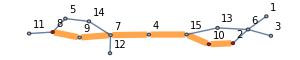
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 80.

```mathematica
gridResult[graph15,  terminals15, treeDreyfusWagner15, resultDreyfusWagner15]
```

```mathematica
edgeWeightSum[Sort/@treeDreyfusWagner15, weightAssociation15]
```

80

#### 100 Verts

```mathematica
({resultDreyfusWagner100, treeDreyfusWagner100} = runDreyfusWagner[graph100, terminals100]);//AbsoluteTiming
resultDreyfusWagner100
```

{13.5463,Null}

652.

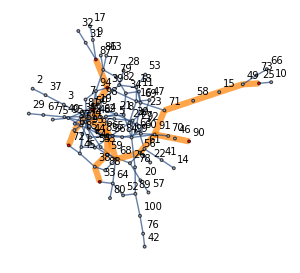
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 652.

```mathematica
gridResult[graph100,  terminals100, treeDreyfusWagner100, resultDreyfusWagner100]
```

```mathematica
edgeWeightSum[Sort/@treeDreyfusWagner100, weightAssociation100]
```

652

#### Stlib

```mathematica
({resultDreyfusWagnerStlibTest, treeDreyfusWagnerStlibTest} = runDreyfusWagner[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
resultDreyfusWagnerStlibTest
```

{0.0491777,Null}

7.

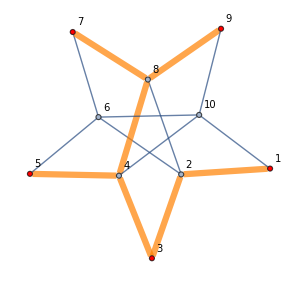
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 7.

```mathematica
gridResult[stlibTestGraph, stlibTestTerminals, treeDreyfusWagnerStlibTest, resultDreyfusWagnerStlibTest]
```

```mathematica
edgeWeightSum[Sort/@treeDreyfusWagnerStlibTest, stlibTestWeights]
```

7

## Approximation algorithms

### 2-approximation (Kou – Markowsky – Berman) [1][2]

#### Description

```mathematica
-Graphics-
-Graphics-
-Graphics-
```

#### Functions

```mathematica
ClearAll[getMetricClosureOfGraphTerminals]

getMetricClosureOfGraphTerminals[graph_Graph, terminals_List]:=
Composition[
Graph[Keys@#, EdgeWeight->#]&,
UndirectedEdge@@#->GraphDistance[graph, Sequence@@#]&/@#&,
Subsets[#, {2}]&
][terminals]
```

```mathematica
ClearAll[runKouMarkowskyBerman]

"
Asymptotic time of first step is O(|T||E| log|V|),
not recommended to use in solving instances with big |T|,
because it builds (full graph) metric closure on T.

Input: graph – weighted Graph instance, terminals – list of terminals.
Output: edges of 2-approximation of steiner tree.
";

runKouMarkowskyBerman[graph_Graph, terminals_]:=
Module[{minSpanningTreeEdges},

minSpanningTreeEdges=
Composition[
EdgeList[#]&,
Subgraph[#, terminals]&,
getMetricClosureOfGraphTerminals[graph, terminals]&
][];

Composition[
Sort/@#&,
FixedPoint[
DeleteCases[#, x_/;
(FreeQ[terminals, x⟦1⟧]∧vertexDegree[x⟦1⟧,#]==1)
∨(FreeQ[terminals, x⟦2⟧]∧vertexDegree[x⟦2⟧,#]==1)
]&,
#]&,

EdgeList@#&,
FindSpanningTree[#]&,
Subgraph[graph, #]&,

UndirectedEdge@@@#&,
DeleteDuplicates[#, ContainsExactly]&,
Flatten[#, 1]&,
Partition[#, 2, 1]&/@#&,
FindShortestPath[graph, #⟦1⟧, #⟦2⟧]&/@#&
][minSpanningTreeEdges]
]
```

### 2-approximation (Mehlhorn) [8]

#### Description

Mehlhorn's algorithm (improvement of previous algorithm):
1. Build Auxilary graph (AG):
	- build Voronoi separation of graph.
	- new graph AG.
	- for all border edges (u, v) add to AG edge (voronoi_center[u], voronoi_center[v]) with weight distance(voronoi_center[u], u) + distance(voronoi_center[v], v) + weight[(u, v)].
2. Find MinSpanningTree in AG.
3. Refind original short-path graph accorgind to spanning tree.
4. Find MinSpanningTree in it.
5. Cut it, to make Steiner-tree.

#### Functions

```mathematica
ClearAll[findPath, findPathRec]

findPath[vert_, anc_] := UndirectedEdge@@@Partition[{findPathRec[vert, anc]}, 2, 1]

findPathRec[vert_, anc_] := Sequence[findPathRec[anc["Part", vert], anc], vert]
findPathRec[-1, anc_] := Nothing
```

```mathematica
ClearAll[runMehlhorn]

runMehlhorn::usage =
"
Asymptotic time of first step is O(|E| log|V|) (binary heap dijkstra), it is not building a full grah on T,
so could be used in solving instances with big |T|.

Input: graph – weighted Graph instance, terminals – list of terminals.
Output: edges of 2-approximation of steiner tree.
";
runMehlhorn[graph_, terminals_]:=
Module[
{
dijVoronoi, vor, sp, auxilaryEdgeWeights
},
dijVoronoi = dijkstraVoronoi[graph, terminals];
vor = dijVoronoi["voronoi"];
sp = dijVoronoi["distance"];

auxilaryEdgeWeights = 
(If[vor["Part", #⟦1⟧]≠vor["Part", #⟦2⟧],
UndirectedEdge[vor["Part", #⟦1⟧],vor["Part", #⟦2⟧], #]->sp["Part", #⟦1⟧] + sp["Part", #⟦2⟧] + edgeWeight[graph, #],
Nothing]&/@EdgeList[graph]);

Composition[
Sort/@#&,
FixedPoint[
DeleteCases[#, x_/;
(FreeQ[terminals, x⟦1⟧]∧vertexDegree[x⟦1⟧,#]==1)
∨(FreeQ[terminals, x⟦2⟧]∧vertexDegree[x⟦2⟧,#]==1)
]&,
#]&,

EdgeList@FindSpanningTree[#]&,
Subgraph[graph, #]&,
Flatten[#]&,
{findPath[#⟦1⟧, dijVoronoi["ancestors"]], findPath[#⟦2⟧, dijVoronoi["ancestors"]],#}&/@#&,
EdgeTags@EdgeList@FindSpanningTree@#&,
Graph[Keys@#, EdgeWeight->#, VertexLabels->"Name"]&
][auxilaryEdgeWeights]
]
```

### Examples

#### 15 Verts

```mathematica
(treeKouMarkowskyBerman15 = runKouMarkowskyBerman[graph15, terminals15]);//AbsoluteTiming
resultKouMarkowskyBerman15 = edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{0.0072318,Null}

199

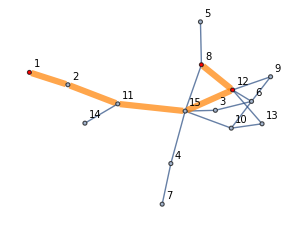
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 199

```mathematica
gridResult[graph15,  terminals15, treeKouMarkowskyBerman15, resultKouMarkowskyBerman15]
```

```mathematica
(treeMehlhorn15 = runMehlhorn[graph15, terminals15]);//AbsoluteTiming
resultMehlhorn15 = edgeWeightSum[treeMehlhorn15, weightAssociation15]
```

{0.0075328,Null}

199

```mathematica
gridResult[graph15,  terminals15, treeMehlhorn15, resultMehlhorn15]
```

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 199

#### 100 Verts

```mathematica
(treeKouMarkowskyBerman100 = runKouMarkowskyBerman[graph100, terminals100]);//AbsoluteTiming
resultKouMarkowskyBerman100 = edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{0.0329868,Null}

787

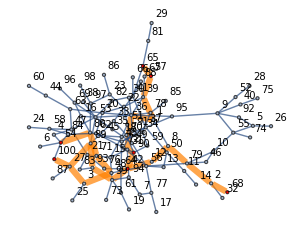
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 787

```mathematica
gridResult[graph100,  terminals100, treeKouMarkowskyBerman100, resultKouMarkowskyBerman100]
```

```mathematica
(treeMehlhorn100 = runMehlhorn[graph100, terminals100]);//AbsoluteTiming
resultMehlhorn100 = edgeWeightSum[treeMehlhorn100, weightAssociation100]
```

{0.0084398,Null}

787

```mathematica
gridResult[graph100,  terminals100, treeMehlhorn100, resultMehlhorn100]
```

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 787

#### Stlib

```mathematica
(treeMehlhornStlibTest = runMehlhorn[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
resultMehlhornStlibTest = edgeWeightSum[treeMehlhornStlibTest, stlibTestWeights]
```

{0.59577,Null}

2143

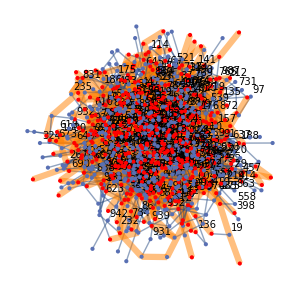
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 2143

```mathematica
gridResult[stlibTestGraph, stlibTestTerminals, treeMehlhornStlibTest, resultMehlhornStlibTest]
```

## Greedy algorithms [6][7]

### SPH

### multiple SPH

## Data Structures

### Left-sided heap

```mathematica
(*On Linked Lists*)
```

#### Linked Lists, recursive realisation

```mathematica
ClearAll[leftistHeapCreate]

(*({priority, element, closest leaf distance, left child, right child})*)
leftistHeapCreate[] := {}
leftistHeapCreate[{elem_, priority_}] := {elem, priority, 0, {}, {}}
```

```mathematica
ClearAll[leftistHeapMeldSwap, leftistHeapMeldRecalcDistance, leftistHeapMeld]

leftistHeapMeldSwap[x:{xe_, xp_, xd_, xl_, xr_ }, y:{ye_, yp_, yd_, yl_, yr_}] := Sequence[x, y]
leftistHeapMeldSwap[x:{xe_, xp_, xd_, xl_, xr_ }, y:{ye_, yp_, yd_, yl_, yr_}]/;xd<yd := Sequence[y, x]
leftistHeapMeldSwap[x_, {}] := Sequence[x, {}]
leftistHeapMeldSwap[{}, y_] := Sequence[y, {}]

leftistHeapMeldRecalcDistance[dist_, x_, y:{ye_, yp_, yd_, yl_, yr_}] := Sequence[yd+1, x, y]
leftistHeapMeldRecalcDistance[dist_, x_, {}] := Sequence[0, x, {}]

leftistHeapMeld[x:{xe_, xp_, xd_, xl_, xr_ }, y:{ye_, yp_, yd_, yl_, yr_}] := 
{xe, xp, leftistHeapMeldRecalcDistance[xd, leftistHeapMeldSwap[xl, leftistHeapMeld[xr, y]]]}

leftistHeapMeld[x:{xe_, xp_, xd_, xl_, xr_ }, y:{ye_, yp_, yd_, yl_, yr_}]/;xp>yp  := leftistHeapMeld[y, x]
leftistHeapMeld[x_, {}] := x
leftistHeapMeld[{}, y_] := y
```

```mathematica
ClearAll[leftistHeapPush]

leftistHeapPush[heap_, {elem_, priority_}] := leftistHeapMeld[heap, leftistHeapCreate[{elem, priority}]]
```

```mathematica
ClearAll[leftistExtractMin]

leftistExtractMin::usage = "Returns {minimum}";
SetAttributes[leftistExtractMin, HoldFirst]
leftistExtractMin[heap_] := 
(Unevaluated[heap]= leftistHeapMeld[heap⟦4⟧, heap⟦5⟧];#)&[heap⟦1⟧]
```

```mathematica
ClearAll[leftistHeapHeapify, leftistHeapHeapifyStep]

leftistHeapHeapify[toAdd:{__List}]:=
Block[{$RecursionLimit=Infinity},
leftistHeapHeapifyStep[toAdd]
]

leftistHeapHeapifyStep[toAdd:{__List}]:=
leftistHeapMeld[leftistHeapHeapifyStep[Take[toAdd, Floor@#]], leftistHeapHeapifyStep[Take[toAdd, -Ceiling@#]]]&[Length[toAdd]/2]  
leftistHeapHeapifyStep[toAdd:{x_List}] := leftistHeapCreate[x]
```

{c,1,1,{a,3,0,{b,5,0,{},{}},{}},{d,4,0,{e,8,0,{},{}},{}}}

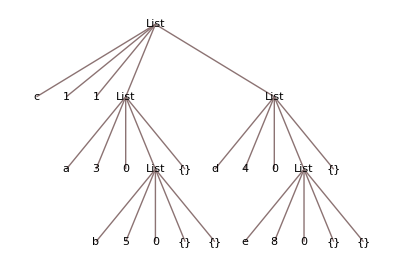

```mathematica
leftistHeapHeapify[{{a, 3}, {b, 5}, {c, 1}, {d, 4}, {e, 8}}]
TreeForm@%
```

```mathematica
n=10000;
tmp = RandomInteger[{1, 1000}, {n, 2}];
(t1 = leftistHeapHeapify[tmp]);//AbsoluteTiming
(Do[leftistExtractMin[t1], n]);//AbsoluteTiming
```

{0.20693,Null}

{1.03638,Null}

```mathematica
ds = CreateDataStructure["PriorityQueue"]
n=10000;
tmp = RandomInteger[{1, 1000}, {n, 2}];
(ds["Push", #]&/@tmp);//AbsoluteTiming
Do[ds["Pop"], n]//AbsoluteTiming
```

DataStructure[PriorityQueue, {Data -> {}}]

{0.0182544,Null}

{0.0439691,Null}

```mathematica
n= 10000;
tmp1 = RandomInteger[{1, 1000}, {n, 2}];
(h1 = leftistHeapHeapify[tmp1]);//AbsoluteTiming
tmp2 = RandomInteger[{1, 1000}, {n, 2}];
(h2 = leftistHeapHeapify[tmp2]);//AbsoluteTiming
(h3 = leftistHeapMeld[h1, h2]);//AbsoluteTiming
```

{0.197472,Null}

{0.210443,Null}

{0.0022746,Null}

```mathematica
n=10000;
ds1 = CreateDataStructure["PriorityQueue"];
tmp1 = RandomInteger[{1, 1000}, {n, 2}];
(ds1["Push", #]&/@tmp1);//AbsoluteTiming
ds2 = CreateDataStructure["PriorityQueue"];
tmp2 = RandomInteger[{1, 1000}, {n, 2}];
(ds2["Push", #]&/@tmp2);//AbsoluteTiming
Do[ds1["Push", ds2["Pop"]], n];//AbsoluteTiming
```

{0.0171505,Null}

{0.0167925,Null}

{0.0463609,Null}

#### Realisation with FixedArray and links

```mathematica
ClearAll[leftistHeapCreate]

(*({priority, element, left distance, left child, right child})*)
leftistHeapCreate[] := {}
leftistHeapCreate[{elem_, priority_}] := 
Module[{ds},
ds = CreateDataStructure["FixedArray", 5];
ds["SetPart", 5, {}];
ds["SetPart", 4, {}];
ds["SetPart", 3, 0];
ds["SetPart", 2, priority];
ds["SetPart", 1, elem];
ds
]
```

```mathematica
ClearAll[leftistHeapMeldSwap, leftistHeapMeldRecalcDistance, leftistHeapMeld]

leftistHeapMeldSwap[orig_, x_, y_] := If[x["Part", 3] < y["Part", 3], (orig["Part", 4] = y; orig["Part", 5] = x;)]
leftistHeapMeldSwap[orig_, {}, y_] := (orig["Part", 4] = y; orig["Part", 5] = {};)
leftistHeapMeldSwap[orig_, x_, {}] := Nothing

leftistHeapMeldRecalcDistance[orig_, x_, y_] := (orig["Part", 3] += 1)
leftistHeapMeldRecalcDistance[orig_, x_, {}] := (orig["Part", 3] = 0)

leftistHeapMeld[x_, y_] := 
If[x["Part", 2]≤y["Part", 2],
(x["Part", 5] = leftistHeapMeld[x["Part", 5], y];
leftistHeapMeldSwap[x, x["Part", 4], x["Part", 5]];
leftistHeapMeldRecalcDistance[x, x["Part", 4], x["Part", 5]];
x),
leftistHeapMeld[y, x]];

leftistHeapMeld[x_, {}] := x
leftistHeapMeld[{}, y_] := y
```

```mathematica
ClearAll[leftistHeapPush]

leftistHeapPush[heap_, {elem_, priority_}] := leftistHeapMeld[heap, leftistHeapCreate[{elem, priority}]]
```

```mathematica
ClearAll[leftistExtractMin]

leftistExtractMin::usage = "Returns {minimum}";
SetAttributes[leftistExtractMin, HoldFirst]
leftistExtractMin[heap_] := 
Module[{min =heap["Part", 1]},
Unevaluated[heap]= leftistHeapMeld[heap["Part", 4], heap["Part", 5]];
min]
```

```mathematica
ClearAll[leftistHeapNormal]

leftistHeapNormal[heap_]:=
{heap["Part", 1], heap["Part", 2], heap["Part", 3], leftistHeapNormal[heap["Part", 4]], leftistHeapNormal[heap["Part", 5]]}

leftistHeapNormal[{}]:={}
```

```mathematica
ClearAll[leftistHeapHeapify, leftistHeapHeapifyStep]

leftistHeapHeapify[toAdd:{__List}]:=
Block[{$RecursionLimit=Infinity},
leftistHeapHeapifyStep[toAdd]
]

leftistHeapHeapifyStep[toAdd:{__List}]:=
leftistHeapMeld[leftistHeapHeapifyStep[Take[toAdd, Floor@#]], leftistHeapHeapifyStep[Take[toAdd, -Ceiling@#]]]&[Length[toAdd]/2]  
leftistHeapHeapifyStep[toAdd:{x_List}] := leftistHeapCreate[x]
```

```mathematica
a =leftistHeapCreate[{1, 5}]
b=leftistHeapCreate[{2, 7}]
```

DataStructure[FixedArray, {Data -> {1, 5, 0, {}, {}}}]

DataStructure[FixedArray, {Data -> {2, 7, 0, {}, {}}}]

```mathematica
c = leftistHeapMeld[a, b]
leftistHeapNormal[c]
```

DataStructure[FixedArray, {Data -> {1, 5, 0, DataStructure[FixedArray, {Data -> {2, 7, 0, {}, {}}}], {}}}]

{1,5,0,{2,7,0,{},{}},{}}

```mathematica
leftistHeapPush[c, {3, 9}]
leftistHeapNormal[c]
```

DataStructure[FixedArray, {Data -> {1, 5, 1, DataStructure[FixedArray, {Data -> {2, 7, 0, {}, {}}}], DataStructure[FixedArray, {Data -> {3, 9, 0, {}, {}}}]}}]

{1,5,1,{2,7,0,{},{}},{3,9,0,{},{}}}

```mathematica
leftistExtractMin[c]
leftistHeapNormal[c]
leftistExtractMin[c]
leftistHeapNormal[c]
leftistExtractMin[c]
leftistHeapNormal[c]
```

1

{2,7,0,{3,9,0,{},{}},{}}

2

{3,9,0,{},{}}

3

{}

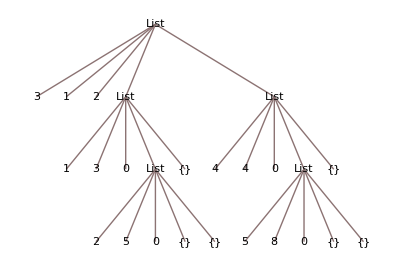

```mathematica
TreeForm@leftistHeapNormal@leftistHeapHeapify[{{1, 3}, {2, 5}, {3, 1}, {4, 4}, {5, 8}}]
```

#### tests

```mathematica
n=10000;
tmp = RandomInteger[{1, 1000}, {n, 2}];
(t1 = leftistHeapHeapify[tmp]);//AbsoluteTiming
(t2 = Reap[Do[Sow[leftistExtractMin[t1]], n], _]⟦2,1⟧);//AbsoluteTiming
```

{0.042133,Null}

{0.16005,Null}

```mathematica
ds = CreateDataStructure["PriorityQueue"]
n=10000;
tmp = RandomInteger[{1, 1000}, {n, 2}];
(Scan[ds["Push", #]&, tmp]);//AbsoluteTiming
Do[ds["Pop"], n]//AbsoluteTiming
```

DataStructure[PriorityQueue, {Data -> {}}]

{0.0200936,Null}

{0.0236643,Null}

```mathematica
session=StartExternalSession["Python"]
```

ExternalSessionObject[…]

```mathematica
ExternalEvaluate[session,
"class fuck:
    def __init__(self, a):
	    self.a = a
    def pa(self):
        return self.a
"]
```

ExternalFunction[…]

```mathematica
ExternalEvaluate[session, "tmp = fuck(1)"]
```

```mathematica
ExternalEvaluate[session, "tmp.pa()"]
```

1

### Dynamic forest

## Local-search algorithms [7]

### Steiner-Vertex Insertion

### Steiner-Vertex Elimination

### Key-Path Exchange

### Key-Vertex Elimination

## References

[1] * Корте Б. Комбинаторная оптимизация. Теория и Алгоритмы / Бернард Корте, Йенс Фиген ; перевод с англ. М.А. Бабенко ; - М. : МЦНМО ; 2015 - 720 с.
[2] Markowski G. A fast algorithm for steiner trees / G. Markowski, L. Kou, L. Berman ; 1981.
[3] ^Fuchs B. Speeding up the Dreyfus-Wagner Algorithmfor minimum Steiner trees / B. Fuchs, W. Kern, X. Wang ; 2007
[4] *^ Fomin F.  Computing Optimal Steiner Trees in Polynomial Space / F. Fomin, F. Grandoni, D. Kratsch, D. Lokshtanov, S.Saurabh ; 2012
[5] Dreyfus S.  The Steiner Problem in Graphs / S. Dreyfus, R. Wagner ; 1971
[6] Plesnik J. Heuristics for the Steiner problem in graphs / J. Plesnik ; 1989
[7] *$ Uchoa E. Fast Local Search for Steiner Trees in Graphs / E. Uchoa, R. Werneck  ; 2010
[8] Mehlhorn K. A Faster Approximation Algorithm for the Steiner Tree Problem in Graphs / K. Mehlhorn ; 1988

^ - more theoretical
$ - more practical
* - really nice paper

## ToDo List

```mathematica
"
- Исправить восстановление дерева в DW
- Эвристики для больших графов.
-- Жадные (old)
-- Локальный поиск (2010)
- Провести тесты
"

"
? - Точная постановка.
? - Алгоритм с 1.53 приближением.
? - Prunning and predprocessing.
? - Ускоренный на separation's DW (2007)
"

"
Done:
- Melhorn
- Дописать в тестер возможность модельных данных
- Протестировать на модельных (библиотечных) данных.
"
```

```mathematica
circuit design,networking,and computational biology
```